Piecewise[{{2^(-Floor[Log[t]]), Floor[Log[t]]<Log[t]}, {Indeterminate, True}}]

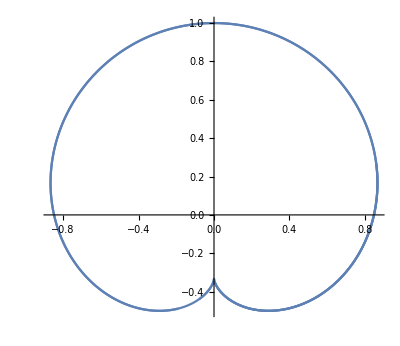

```mathematica
ClearAll["Global`*"]
f[n_]:=n*4;
g[n_]:=n/2^Floor[Log[n]];
Print[FullSimplify[g'[t]]];
F[x_,y_,t_]:=Sin[(2*Pi*f[t])/(2^Floor[Log[4*t]])-(2*Pi*t)/(2^Floor[Log[t]])]-y*(Sin[(2*Pi*t*4)/(2^Floor[Log[4*t]])]-Sin[(2*Pi*t)/(2^Floor[Log[t]])])-x*(Cos[(2*Pi*t*4)/(2^Floor[Log[4*t]])]-Cos[(2*Pi*t)/(2^Floor[Log[t]])]);
Fd[x_,y_,t_]:= 2*Pi*(
(f'[t]/(2^Floor[Log[f[t]]]))*(Cos[(2*Pi*t)*g'[t]-(2*Pi*t*4)/(2^Floor[Log[4*t]])]-y*Cos[(2*Pi*t*4)/(2^Floor[Log[4*t]])]+x*Sin[(2*Pi*t*4)/(2^Floor[Log[4*t]])])
-(1/(2^Floor[Log[t]]))*(Cos[(2*Pi*t)/(2^Floor[Log[t]])-(2*Pi*t*4)/(2^Floor[Log[4*t]])]-y*Cos[(2*Pi*t)/(2^Floor[Log[t]])]+x*Sin[(2*Pi*t)/(2^Floor[Log[t]])])
);
parametricFunc[t_]:={x,y}/.(Solve[F[x,y,t]==0&&Fd[x,y,t]==0,{x,y}]);
ParametricPlot[parametricFunc[t],{t,0,2}]
```